## Assymmetric Molecule: Dispersion

```mathematica
ClearAll["Global`*"]
Ω[μ_]:=({{ω1[μ], -J12, 0}, {-J12, ω2[μ], -J23}, {0, -J23, ω3[μ]}});
```

```mathematica
ω1[μ_]:=ω0 +d1×μ + d2/2 μ^2;
ω2[μ_]:=ω0 +D1×(2μ) + D2/2(2μ)^2;
ω3[μ_]:=ω0+d1×μ + d2/2 μ^2 ;
```

```mathematica
d1 = 400;
D1 = 400/2.03;
d2 =-0.015;
D2 = 0.015;
ω0 = 0;
J12=2;
J23=2;
```

```mathematica
freqs= Sort[Eigenvalues[Ω[μ]]];
ωS[μ_]:=freqs[[1]];
ωC[μ_]:=freqs[[2]];
ωAS[μ_]:=freqs[[3]];
```

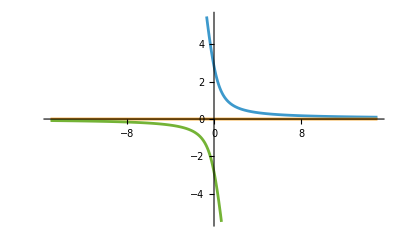

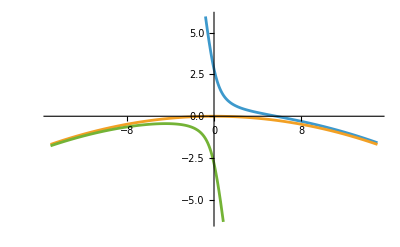

```mathematica
Plot[{ωAS[μ]-ωC[μ],ωC[μ]-ωC[μ],ωS[μ]-ωC[μ]}, {μ,-15,15}]
Plot[{ωAS[μ]-d1×μ,ωC[μ]-d1×μ,ωS[μ]-d1×μ}, {μ,-15,15}]
```